# Simulations

This documentation applies to SpinDynamica v3.10

Part 1 of this documentation should be read first.

SpinDynamica includes several routines which perform some common numerical simulation tasks in magnetic resonance, with a minimum of user coding.

more advanced topics use this colour

## Setup

The code in this notebook requires initialization of SpinDynamica, and the current spin system, as described in part 1

```mathematica
Needs["SpinDynamica`"];
SetSpinSystem[1]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

## Generalities

### colour code

topics suitable for beginners use this colour

more advanced topics which may be skipped by beginners use this colour

### Options and defaults

All SpinDynamica routines use the standard structure of Mathematica objects. Routines are summoned using replacement rules of the form a→b for the optional parameters (the symbol → may be typeset using [esc]->[esc] where [esc] is the “escape” key). If these specifications are omitted, the routine uses defaults which are often appropriate.

For example, consider the routine Trajectory discussed below. The default settings for the Trajectory options may be examined as follows:

```mathematica
Options[Trajectory]
```

{OperatorBasis:>ZeemanKetBraOperatorBasis[],Basis:>ZeemanBasis[],NormalizationFactor→None,UseMatrixExpWhenPossible→True,UseHilbertSpaceWhenPossible→True,UseDiagonalizationWhenPossible→False,InitialTimePoint→0,FinalTimePoint→Automatic,BackgroundGenerator→None,EnsembleAverage→False,InterpolationPoints→500,AccuracyGoal→10,PrecisionGoal→10,MaxSteps→Automatic,MaxStepSize→Automatic,Simulations`Simulations`Private`InterpolationStepSize→1.×10^-6,Chronology:>$Chronology,Parallel→True,MaxBatchSize→128,MinimumRecommendedUserLevel→2}

Most of these option settings refer to details of the numerical algorithms and are beyond the scope of this introductory document. In most cases, the defaults work fine.

The default settings for one or more options may be overridden at the time of use by specifying the values explicitly. For example, consider the following syntax:

```mathematica
SetSpinSystem[1];
Trajectory[opI["z"]->opI["z"],{2π opI["x"],1},InitialTimePoint->1]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

TrajectoryFunction[{{1.,2.}}, <>]

The explicit instruction InitialTimePoint→1 supersedes the default setting InitialTimePoint→0.

Options of the type parameter→value may be given in any order.

#### changing default settings

The default settings of an option may be changed for the entire Mathematica session by using SetOptions, for example

```mathematica
SetOptions[Trajectory, InterpolationPoints->1000];
```

This changes the default setting for the chosen parameter:

```mathematica
Options[Trajectory]
```

{OperatorBasis:>ZeemanKetBraOperatorBasis[],Basis:>ZeemanBasis[],NormalizationFactor→None,UseMatrixExpWhenPossible→True,UseHilbertSpaceWhenPossible→True,UseDiagonalizationWhenPossible→False,InitialTimePoint→0,FinalTimePoint→Automatic,BackgroundGenerator→None,EnsembleAverage→False,InterpolationPoints→1000,AccuracyGoal→10,PrecisionGoal→10,MaxSteps→Automatic,MaxStepSize→Automatic,Simulations`Simulations`Private`InterpolationStepSize→1.×10^-6,Chronology:>$Chronology,Parallel→True,MaxBatchSize→128,MinimumRecommendedUserLevel→2}

```mathematica
InterpolationPoints/.Options[Trajectory]
```

1000

The parameter InterpolationPoints now takes the value 1000, if it is not specified explicitly in the call to Trajectory.

### BackgroundGenerator

An important option for most of the simulation routines is BackgroundGenerator. This specifies an evolution generator which runs as a “background” through the entire calculation and which is combined automatically with the event specifications.

In most cases, the BackgroundGenerator parameter is used for the “internal” Hamiltonian and relaxation superoperator, while the sequence of events specifies the interactions with applied magnetic fields.

Examples of BackgroundGenerator are given in the documentation for the individual functions below.

### EnsembleAverage

An important option for most of the routines is EnsembleAverage. This allows repetition of the calculations with a variable taking a defined set of values, and the results superposed afterwards.

Examples of EnsembleAverage are given in the documentation for the individual functions below.

#### general syntax for EnsembleAverage

The general syntax for the EnsembleAverage option is

EnsembleAverage → {var, {{val1, weight1}, {val2, weight2}..}}

where var is a symbol, the list {val1,val2..} contains a set of values taken by the symbol, and the results of the simulations are multiplied by the weights {weight1,weight2..} and added together.

#### abbreviated syntax

If the weights are omitted, they are assumed to be equal, and to add up to 1. For example:

EnsembleAverage → {var, {val1,val2,val3}}

is equivalent to

EnsembleAverage → {var, {{val1,1/3},{val2,1/3}, {val3,1/3}}}

#### EnsembleAverage of a multidimensional variable

Each value of the ensemble variable {val1,val2,val3} may be a list of numbers itself. For example,  syntax of the following form might be used for simulating an NMR imaging experiment:

EnsembleAverage → {r, {{{x1,y1,z1}, w1}, {{x2,y2,z2}, w2}, {{x3,y3,z3}, w3}}}

Here the Cartesian position of a volume element is denoted r, and averaging is conducted over three points with coordinates {x1,y1,z1}, {x2,y2,z2} and {x3,y3,z3}. The weights {w1,w2,w3} could be used to encode the relative spin density at three points. This syntax could readily be extended to any numbers of sampled points. In general specifications of this form are best constructed using the very general structural operations provided by Mathematica.

#### CarouselAverage

If Signal1D is used to calculate the signal in the presence of a periodic background generator, the option CarouselAverage→True may be used to take the average over all phases of the periodic background generator, in a computationally efficient way. This option may be used at the same time as EnsembleAverage.

See Signal1D for examples.

#### MaxBatchSize

The computation of an ensemble average is normally performed in batches, in order to conserve memory. All members of a single batch are computed and combined, before proceeding to the next batch. The option MaxBatchSize may be used to control the maximum number of members in each batch.

The option setting MaxBatchSize→Infinity forces computation in a single batch.

The default setting is MaxBatchSize→128

There should be no need to control MaxBatchSize in normal use.

### Parallel

In SpinDynamica v2.6.0 and later, EnsembleAverage is implemented automatically by launching parallel kernels and executing simultaneous SpinDynamica computations. The results of the parallel computations are combined automatically when all computations are finished.

#### disabling parallel computation

The option Parallel→False may be used to disable parallel computation, leading to sequential execution of the computations in EnsembleAverage.

#### controlling the number of parallel kernels

The option Parallel→n, where n is an integer, executes the code on n parallel kernels. The default setting Parallel→True, or Parallel→Automatic, uses the maximum number of parallel kernels available on the computation platform.

## Trajectory

Trajectory tracks the evolution of one or more operator expectation values under a sequence of events, starting from any initial value for the spin density operator.

The sequence of events may be specified using PulseSequence syntax, or explicit syntax, or a mix (see part 1).

The output of Trajectory is a TrajectoryFunction, which may then be evaluated at any time during the computed range.

#### single event

The following instruction sets the spin system to a single spin-1/2, and then calculates the trajectory of the expectation value of I_y, starting with a density operator I_z, during a 2π pulse acting for 1 second:

```mathematica
SetSpinSystem[1];
traj=Trajectory[opI["z"]->opI["y"],Pulse[{2π,"x"},PulseDuration->1]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

TrajectoryFunction[{{0,1.}}, <>]

The output of Trajectory is not a single number or a list of numbers, but a TrajectoryFunction that may be evaluated at any time point in the computed range, for example

```mathematica
traj[0.3]
```

-0.951057

Evaluation of the TrajectoryFunction may be performed at a set of times by using the Map function of Mathematica (abbreviated /@):

```mathematica
traj/@{0.3,0.4,0.5}
```

{-0.951057,-0.587785,0}

The complete trajectory may be plotted using the Mathematica Plot routine:

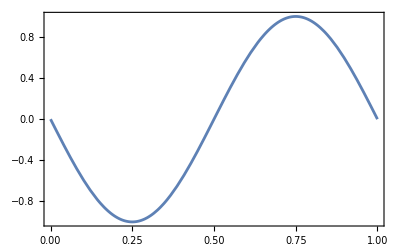

```mathematica
Plot[traj[t],{t,0,1}]
```

The output TrajectoryFunction cannot be evaluated outside its range. Attempt to evaluate outside the computed range will generate a warning and a zero result:

```mathematica
traj[1.2]
```

TrajectoryFunction::outofrange: time point 1.2 does not lie in the interval between 0. and 1.

0

TrajectoryFunction::outofrange: time point -0.999939 does not lie in the interval between 0. and 1.

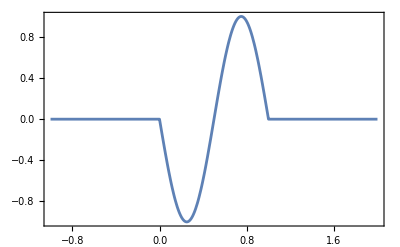

```mathematica
Plot[traj[t],{t,-1,2}]
```

#### sequences of events

Trajectory may be used over an arbitrary sequence of events. For example:

```mathematica
traj=Trajectory[opI["z"]->opI["y"],
PulseSequence[{Pulse[{π,"x"}],Pulse[{2π,"-x"}],Pulse[{π,"x"}]},NutationFrequency->2π]
]
```

TrajectoryFunction[{{0,2.}}, <>]

The trajectory may be plotted using the Mathematica Plot routine:

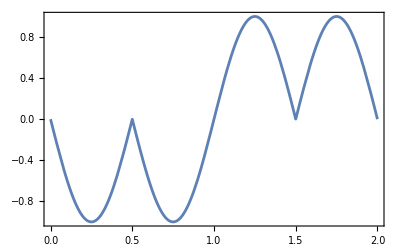

```mathematica
Plot[traj[t],{t,0,2}]
```

The TrajectoryFunction consists of distinct ranges which are spliced together.  This is handled internally and requires no user intervention. Very complex sequences may be handled, for example:

```mathematica
sequence=Repeat[PulseSequence[{Pulse[{π/3,"x"}],Pulse[{π/6,2π/3}],Pulse[{π/2,"x"}]},NutationFrequency->2π],30];
traj=Trajectory[opI["z"]->opI["y"],sequence]
```

TrajectoryFunction[{{0,15.}}, <>]

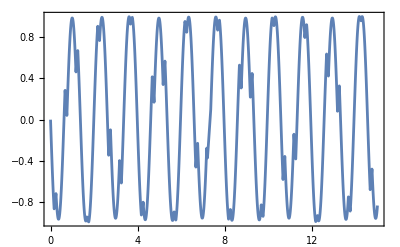

```mathematica
Plot[traj[t],{t,0,Duration[sequence]}]
```

Note the use of Duration to set the range of the plot in a convenient way.

#### multiple expectation values; 3D trajectories

Trajectory calculates the expectation values of any number of operators at the same time (starting from the same initial condition), for example:

```mathematica
{xtraj,ytraj,ztraj}=
Trajectory[opI["z"]->{opI["x"],opI["y"],opI["z"]},
PulseSequence[{Pulse[{π/2,"x"}],Pulse[{π,"y"}],Pulse[{π/2,"x"}]},NutationFrequency->2π,AmplitudeFactor->0.8]
]
```

{TrajectoryFunction[{{0,1.}}, <>],TrajectoryFunction[{{0,1.}}, <>],TrajectoryFunction[{{0,1.}}, <>]}

The three trajectories may be plotted at the same time using the Mathematica Plot routine:

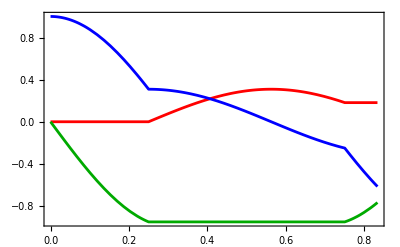

```mathematica
Plot[{xtraj[t],ytraj[t],ztraj[t]},{t,0,5/6},PlotStyle->{Red,Darker[Green],Blue}]
```

The Mathematica routine ParametricPlot3D may be used to plot these trajectories in 3D space:

```mathematica
ParametricPlot3D[{xtraj[t],ytraj[t],ztraj[t]},{t,0,5/6},PlotStyle->Thick,PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

The trajectory may be superposed on a transparent 3D sphere using the graphical SpinDynamica object SphereAndAxes[]:

```mathematica
Show[
SphereAndAxes[],
ParametricPlot3D[
{xtraj[t],ytraj[t],ztraj[t]},{t,0,5/6},
Axes->None,PlotStyle->{{Thick,Blue}}
],
Boxed->False
]
```

-Graphics3D-

In most Mathematica front ends, you can use mouse drags to rotate the object on the screen. This functionality allows the rapid calculation of 3D graphical representations of spin dynamical evolution.

#### BackgroundGenerator

Setting the BackgroundGenerator option causes an evolution generator to act throughout the sequence, in combination with the specified events, without being specified explicitly during each event

For example, this code simulates the trajectory of z-magnetization through a composite pulse sequence, in the absence of a resonance offset:

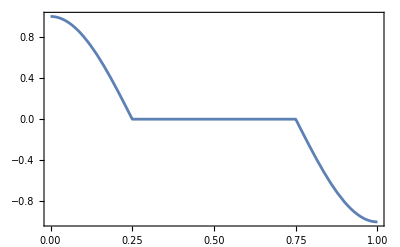

```mathematica
ztraj1=Trajectory[opI["z"]->opI["z"],
PulseSequence[{Pulse[{π/2,"x"}],Pulse[{π,"y"}],Pulse[{π/2,"x"}]},NutationFrequency->2π]
];
Plot[ztraj1[t],{t,0,1}]
```

A resonance offset may be included by using BackgroundGenerator:

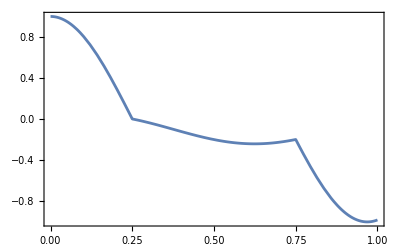

```mathematica
ztraj2=Trajectory[opI["z"]->opI["z"],
PulseSequence[{Pulse[{π/2,"x"}],Pulse[{π,"y"}],Pulse[{π/2,"x"}]},NutationFrequency->2π],
BackgroundGenerator->2π 0.1 opI["z"]
];
Plot[ztraj2[t],{t,0,1}]
```

The same effect is achieved by adding the offset Hamiltonian to all events. However the use of BackgroundGenerator is more compact and convenient, and also evaluates faster in many cases.

```mathematica
ztraj3=Trajectory[opI["z"]->opI["z"],
{{2π opI["x"]+2π 0.1 opI["z"],1/4},
{2π opI["y"]+2π 0.1 opI["z"],1/2},
{2π opI["x"]+2π 0.1 opI["z"],1/4}}
];
Plot[ztraj3[t],{t,0,1}]
```

-Graphics-

The magnetization trajectories under this sequence of off-resonance pulses may be plotted using ParametricPlot3D, as before:

```mathematica
{xtraj,ytraj,ztraj}=Trajectory[
opI["z"]->{opI["x"],opI["y"],opI["z"]},
PulseSequence[{Pulse[{π/2,"x"}],Pulse[{π,"y"}],Pulse[{π/2,"x"}]},NutationFrequency->2π],
BackgroundGenerator->2π 0.2 opI["z"]
];
Show[
SphereAndAxes[],
ParametricPlot3D[
{xtraj[t],ytraj[t],ztraj[t]},{t,0,5/6},
Axes->None,PlotStyle->{{Thick,Blue}}
],
Boxed->False
]
```

-Graphics3D-

BackgroundGenerator is often used to specify the internal Hamiltonians or relaxation properties of complex spin systems.

#### ShapedPulse

A radiofrequency field subjected to a linear frequency sweep may be coded using ShapedPulse:

```mathematica
ChirpDuration=200 10^-3;
ChirpWidth=2π 10^3;
ChirpAmplitude=2π 100;
ChirpPulse=ShapedPulse[ChirpDuration,{tloc,{ChirpAmplitude,0,ChirpWidth (tloc/ChirpDuration)}}];
```

TrajectoryFunction[{{0,200.×10^-3}}, <>]

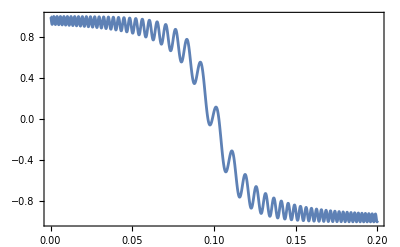

```mathematica
traj=Trajectory[opI["z"]->opI["z"],ChirpPulse]
Plot[traj[t],{t,0,ChirpDuration}]
```

The trajectory reveals a near-adiabatic inversion of the magnetization as the rf field sweeps through.

Consecutive chirps are easily simulated:

```mathematica
traj=Trajectory[opI["z"]->opI["z"],Repeat[ChirpPulse,4]]
```

TrajectoryFunction[{{0,800.×10^-3}}, <>]

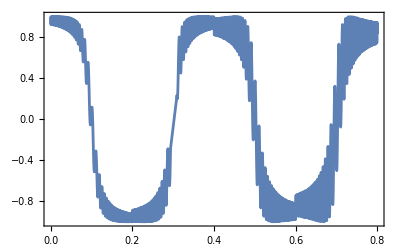

```mathematica
Plot[traj[t],{t,0,4 ChirpDuration}]
```

As before, Mathematica’s 3D routines are easily used to plot the magnetization trajectories during the chirp:

```mathematica
{xtraj,ytraj,ztraj}=Trajectory[
opI["z"]->{opI["x"],opI["y"],opI["z"]},
ChirpPulse
];
Show[
SphereAndAxes[],
ParametricPlot3D[
{xtraj[t],ytraj[t],ztraj[t]},{t,0,Duration[ChirpPulse]},
Axes->None,PlotStyle->{{Thick,Blue}}
],
Boxed->False
]
```

-Graphics3D-

#### EnsembleAverage

The EnsembleAverage option may be used to take the weighted sum of many trajectories.

For example, consider this simulation of the nutation of z-magnetization under a rf field along the x-axis:

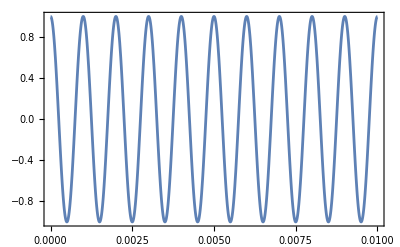

```mathematica
traj=Trajectory[opI["z"]->opI["z"],{2π 10^3 opI["x"],10 10^-3}];
Plot[traj[t],{t,0,10 10^-3}]
```

Suppose now that you wish to take the average of two simulations, using different values of the rf field, expressed as a nutation frequency. Suppose that the two nutation frequencies are 1.0 kHz and 1.2 kHz. Define a nutation frequency variable ωnut, and perform the average computation using EnsembleAverage:

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder].

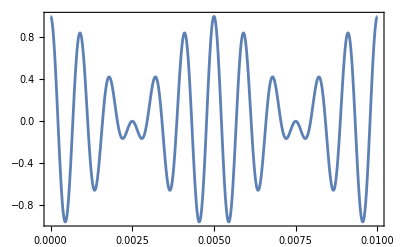

```mathematica
traj=Trajectory[opI["z"]->opI["z"],{ωnut opI["x"],10 10^-3},
EnsembleAverage->{ωnut,{2π 10^3,2π 1.2 10^3}}
];
Plot[traj[t],{t,0,10 10^-3}]
```

If you want to average over 100 simulations, using equally spaced values of the rf nutation frequency between 1.0 kHz and 1.2 kHz, this is easily done using the Mathematica Subdivide routine:

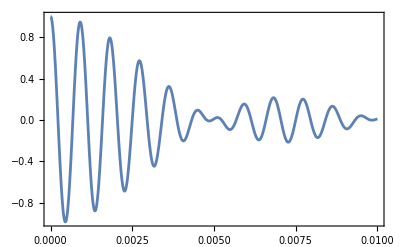

```mathematica
traj=Trajectory[opI["z"]->opI["z"],{ωnut opI["x"],10 10^-3},
EnsembleAverage->{ωnut,2π 10^3 Subdivide[1,1.2,100]}
];
Plot[traj[t],{t,0,10 10^-3}]
```

EnsembleAverage may also be combined with the powerful routines in Mathematica for generating and sampling random distributions. For example, an inhomogeneous rf field is more accurately by simulated by constructing a normally distributed ensemble of rf nutation frequencies. The RandomVariate routine of Mathematica may be used to generate a set of 1000 random values sampled from a normal distribution. In the example below the distribution is centred at 1 kHz with a standard deviation of 100 Hz:

```mathematica
ωnutvals=RandomVariate[NormalDistribution[2π 10^3,2π 100],1000];
```

You can examine the distribution of values using Histogram

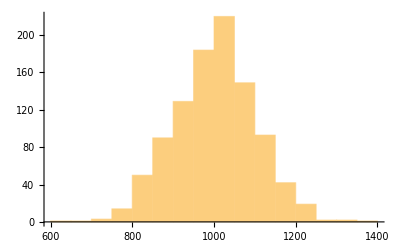

```mathematica
Histogram[ωnutvals/(2π)]
```

The following syntax sums together the trajectories for these 1000 values of the nutation frequency, with equal weights. The result simulates the effect of rf inhomogeneity causing a decay of the nutation curve:

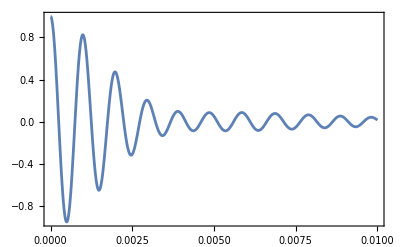

```mathematica
traj=Trajectory[opI["z"]->opI["z"],{ωnut opI["x"],10 10^-3},
EnsembleAverage->{ωnut,ωnutvals}
];
Plot[traj[t],{t,0,10 10^-3},PlotRange->All]
```

The ensemble variable (ωnut in the example above) may be contained in any of the event specifications or any of the options, including the BackgroundGenerator. The example below shows the simulation of a spin echo. An inhomogeneous magnetic field is simulated by setting the resonance offset to a normally distributed random variable:

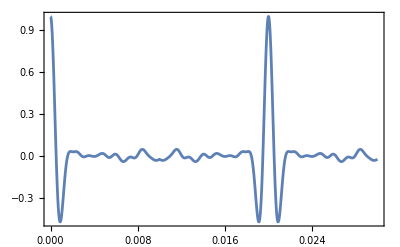

```mathematica
traj=Trajectory[
opI["x"]->opI["x"],
{{None,10 10^-3},
RotationSuperoperator[{π,"x"}],
{None,20 10^-3}},
BackgroundGenerator->Ω opI["z"],
EnsembleAverage->
{Ω ,
RandomVariate[NormalDistribution[2π 500,2π 200],1000]}
];
Plot[traj[t],{t,0,30 10^-3},PlotRange->All]
```

#### NormalizationFactor

The option NormalizationFactor→normfac may be used to divide the output of Trajectory by normfac. The default value is 1.

The example below shows the result of two calculations, one using the default value of NormalizationFactor, and one with a user-specified value.

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

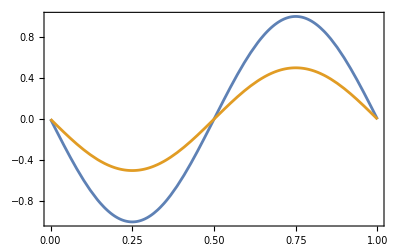

```mathematica
SetSpinSystem[1];
traj1=Trajectory[opI["z"]->opI["y"],{2π opI["x"],1}];
traj2=Trajectory[opI["z"]->opI["y"],{2π opI["x"],1},NormalizationFactor->2];
Plot[{traj1[t],traj2[t]},{t,0,1}]
```

A frequent use of this is to normalize the result of a calculation against the thermal equilibrium signal. For example, the lines below determine the thermal equilibrium density operator for protons at a Larmor frequency of -500 MHz and temperature 300 K, and then determine the thermal equilibrium z-magnetization:

```mathematica
SetSpinSystem[1];
ω0=2π (-500 10^6);
Temperature=300;
ρeq=ThermalEquilibriumDensityOperator[ω0 opI["z"],Temperature];
Meq=OperatorAmplitude[ρeq->opI["z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

0.00003999

In the following simulation, the trajectory of z-magnetization is simulated during a 360° pulse applied to a thermal equilibrium state, and normalized against the thermal equilibrium magnetization:

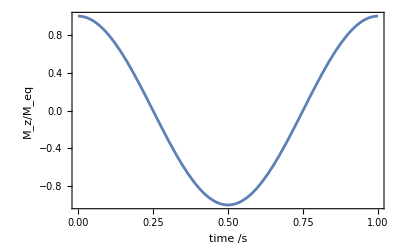

```mathematica
traj=Trajectory[ρeq->opI["z"],{2π opI["x"],1},NormalizationFactor->Meq];
Plot[traj[t],{t,0,1},FrameLabel->{"time /s","M_z/M_eq"}]
```

Note the use of the labelling.

#### InitialTimePoint and FinalTimePoint

By definition, the origin of the running time variable is at the start of the sequence. This may be changed, if desired.

The InitialTimePoint may be used to set the value of the global time variable at the start of the sequence:

```mathematica
SetSpinSystem[1];
traj=Trajectory[opI["z"]->opI["y"],{2π opI["x"],1},InitialTimePoint->2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

TrajectoryFunction[{{2.,3.}}, <>]

the resulting trajectory is only defined within the corresponding range of the time variable:

TrajectoryFunction::outofrange: time point 0.0000817143 does not lie in the interval between 2. and 3.

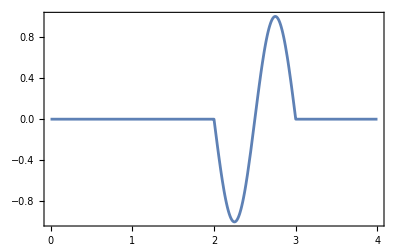

```mathematica
Plot[traj[t],{t,0,4}]
```

The option FinalTimePoint may be used to set the final time point of the sequence of events, instead.

```mathematica
traj=Trajectory[opI["z"]->opI["y"],{2π opI["x"],1},FinalTimePoint->2]
```

TrajectoryFunction[{{1.,2.}}, <>]

TrajectoryFunction::outofrange: time point 0.0000817143 does not lie in the interval between 1. and 2.

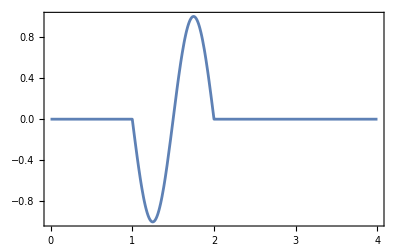

```mathematica
Plot[traj[t],{t,0,4}]
```

If both are used at the same time, the interval between the time points must be consistent with the duration of the event:

```mathematica
Trajectory[opI["z"]->opI["y"],{2π opI["x"],1},FinalTimePoint->2,InitialTimePoint->0]
```

Trajectory::tlimsincompat: The interval between the InitialTimePoint and FinalTimePoint is incompatible with the event duration.

$Failed

#### MaxStepSize and MaxSteps

The spin dynamics during time-dependent events is calculated using the NDSolve routine of Mathematica. Any of the options used by NDSolve may be supplied to Trajectory. See the Mathematica documentation for NDSolve to elucidate the possible arguments.

One of the most important arguments for NDSolve are:
1.  MaxStepSize which governs the maximum timestep used when solving the differential equations. The default used in SpinDynamica is Automatic. The adaptive numerical integrators of Mathematica will then try to choose the optimal MaxStepSize. However, in some cases, the MaxStepSize should be set manually. This could be in cases of large or strongly oscillating Hamiltonians. If in doubt some experimentation is needed.  
2. MaxSteps governs the largest number of steps used to divide up a time-dependent event, when using NDSolve for numerical solution of the differential equations. The default in SpinDynamica is Automatic. This may need to be increased in some cases.

## TransformationAmplitude

TransformationAmplitude provides the end result of a Trajectory calculation, i.e. an answer to questions such as “how much of operator b is generated when density operator a evolves under a sequence of events”?

#### single event

For example, evolving I_z under a 180° pulse inverts the sign of -I_z:

```mathematica
TransformationAmplitude[opI["z"]->opI["z"],Pulse[{π,"x"}]]
```

-1.

Applying a 90° pulse to I_z with zero phase generates -I_y:

```mathematica
TransformationAmplitude[opI["z"]->opI["y"],Pulse[{π/2,"x"}]]
```

-1.

#### several events

Any sequence of events may be used:

```mathematica
TransformationAmplitude[opI["z"]->opI["z"],
{Delay[1/2],
Pulse[{π/3,"x"}],
Delay[1/2]}
]
```

0.5

#### EnsembleAverage

EnsembleAverage may be used with TransformationAmplitude to calculate the average over a set of values for any parameter. This computation takes the average over a distribution of rf field deviations, evenly distributed between -20% and +10%:

```mathematica
rfampvalues=Range[0.8,1.1,0.01]
```

{0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1}

```mathematica
TransformationAmplitude[opI["z"]->opI["z"],
Pulse[{π,"x"},AmplitudeFactor->rfampfac],
EnsembleAverage->{rfampfac,rfampvalues}
]
```

-0.949155

#### multiple TransformationAmplitude calculations

TransformationAmplitude may calculate several transformations at the same time, all starting from the same initial condition:

```mathematica
TransformationAmplitude[opI["z"]->{opI["x"],opI["y"],opI["z"]},Pulse[{π,"x"},AmplitudeFactor->rfampfac],
EnsembleAverage->{rfampfac,rfampvalues}
]
```

{0,-0.150331,-0.949155}

#### NormalizationFactor

The option NormalizationFactor→normfac may be used to divide the output of TransformationAmplitude by normfac. The default value is 1.

The example below shows the result of two calculations, one using the default value of NormalizationFactor, and one with a user-specified value.

```mathematica
SetSpinSystem[1];
TransformationAmplitude[opI["z"]->opI["z"],Pulse[{π,"x"}]]
TransformationAmplitude[opI["z"]->opI["z"],Pulse[{π,"x"}],
NormalizationFactor->2
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

-1.

-0.5

## TransformationAmplitudeBounds

TransformationAmplitudeBounds provides the minimum and maximum possible TransformationAmplitude for a unitary transformation (corresponding to a pulse sequence neglecting relaxation).

For the theory of bounds on transformation amplitudes, see O. W. Sørensen, J. Magn. Reson. 86, 435-440 (1990), M. H. Levitt, J. Magn. Reson. 99, 1 (1992) and M. H. Levitt, J. Magn. Reson. 262, 91 (2016).

For example, the calculation below shows that the polarization of an I-spin can be fully converted into the polarization of an S-spin:

```mathematica
SetSpinSystem[2];
TransformationAmplitudeBounds[opI[1,"z"]->opI[2,"z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

{-1,1}

Surprisingly, it is not possible to obtain more polarization on the S-spin if there are two I-spins:

```mathematica
SetSpinSystem[3];
TransformationAmplitudeBounds[opI[{1,2},"z"]->opI[3,"z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

{-1,1}

However, it is possible to obtain 50% more polarization on the S-spin if there are three I-spins:

```mathematica
SetSpinSystem[4];
TransformationAmplitudeBounds[opI[{1,2,3},"z"]->opI[4,"z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2}},BasisLabels→Automatic].

{-3/2,3/2}

The same maximum transformation applies for four I-spins:

```mathematica
SetSpinSystem[5];
TransformationAmplitudeBounds[opI[{1,2,3,4},"z"]->opI[4,"z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2},{5,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2},{5,1/2}},BasisLabels→Automatic].

{-3/2,3/2}

Five I-spins gives a tiny bit more:

```mathematica
SetSpinSystem[6];
TransformationAmplitudeBounds[opI[{1,2,3,4,5},"z"]->opI[4,"z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2},{5,1/2},{6,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2},{5,1/2},{6,1/2}},BasisLabels→Automatic].

{-15/8,15/8}

## TransformationAmplitudeTable

TransformationAmplitudeTable allows construction of a set of TransformationAmplitude values, with a variable parameter taking a set of equally-spaced values, similar to the Table routine of Mathematica.

The variation of multiple parameters is also possible.

The output of TransformationAmplitudeTable may be plotted using ListPlot (for one variable) or ListContourPlot (for two variables).

By default, TransformationAmplitudeTable uses parallel evaluation over all available kernels.

#### basic functionality

The basic syntax of TransformationAmplitudeTable is as follows:

TransformationAmplitudeTable[a→b, events, {n,nmin,nmax,dn}, options]

where a is the initial density operator, b is the target density operator (which may also be a list of several operators, as in Trajectory), events contains the specifications for the evolution events, and n is the iteration variable, which runs between nmin and nmax in steps of dn. If dn is omitted, then dn=1 is assumed. The options may contain a set of replacement rules, including specifications for BackgroundGenerator and EnsembleAverage. Any of the events or the BackgroundGenerator specifications may depend on n.

For example, the following syntax plots the z-inversion performance of a composite pulse against the rf amplitude factor:

```mathematica
SetSpinSystem[1];
TransformationAmplitudeTable[
opI["z"]->opI["z"],
PulseSequence[{Pulse[{π/2,"x"}],Pulse[{π,"y"}],Pulse[{π/2,"x"}]},
AmplitudeFactor->ampfac],
{ampfac,0,2,0.05}
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

{{0.,1.},{0.05,0.975452},{0.1,0.903311},{0.15,0.787953},{0.2,0.636271},{0.25,0.457107},{0.3,0.260531},{0.35,0.0570442},{0.4,-0.143237},{0.45,-0.33133},{0.5,-0.5},{0.55,-0.644199},{0.6,-0.761271},{0.65,-0.850937},{0.7,-0.91504},{0.75,-0.957107},{0.8,-0.981763},{0.85,-0.99406},{0.9,-0.998802},{0.95,-0.999924},{1.,-1.},{1.05,-0.999924},{1.1,-0.998802},{1.15,-0.99406},{1.2,-0.981763},{1.25,-0.957107},{1.3,-0.91504},{1.35,-0.850937},{1.4,-0.761271},{1.45,-0.644199},{1.5,-0.5},{1.55,-0.33133},{1.6,-0.143237},{1.65,0.0570442},{1.7,0.260531},{1.75,0.457107},{1.8,0.636271},{1.85,0.787953},{1.9,0.903311},{1.95,0.975452},{2.,1.}}

By default, the value of the variable parameter is used as an x-coordinate. The output may be plotted using ListPlot:

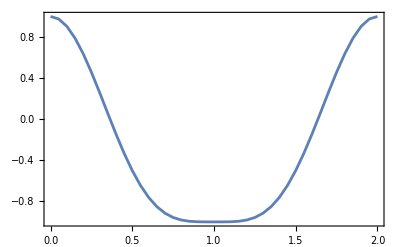

```mathematica
ListPlot[%]
```

The following syntax may be used to specify the number of increments in the variable parameter:

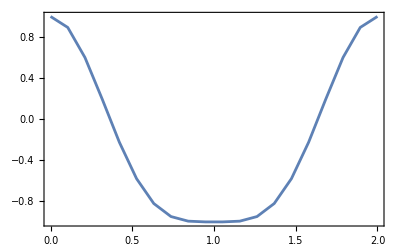

```mathematica
TransformationAmplitudeTable[
opI["z"]->opI["z"],
PulseSequence[{Pulse[{π/2,"x"}],Pulse[{π,"y"}],Pulse[{π/2,"x"}]},
AmplitudeFactor->ampfac],
{ampfac,0,2,{20}}
];
ListPlot[%]
```

#### TableCoordinates

The x-coordinates of TransformationAmplitudeTable may be specified by setting the TableCoordinates option to any expression containing the variable parameter. The example below varies the amplitude factor for a composite pulse but plots it in units of %:

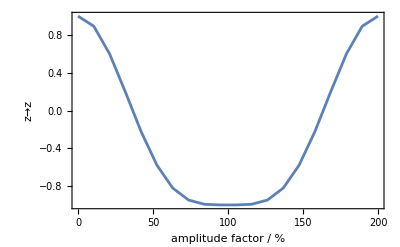

```mathematica
TransformationAmplitudeTable[
opI["z"]->opI["z"],
PulseSequence[{Pulse[{π/2,"x"}],Pulse[{π,"y"}],Pulse[{π/2,"x"}]},
AmplitudeFactor->ampfac],
{ampfac,0,2,{20}},
TableCoordinates->ampfac*100
];
ListPlot[%,FrameLabel->{"amplitude factor / %","z→z"}]
```

A common setting for TableCoordinates is the duration of a pulse sequence, or part of a pulse sequence. In the example below, a 2-spin-1/2 system is constructed, and the spin Hamiltonian H0 set to that of a strongly-coupled AB system. A spin echo pulse sequence is defined, and the echo modulation curve calculated using TransformationAmplitudeTable. TableCoordinates is used to invest the calculated points with the duration of the spin-echo sequence.

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-30) opI[2,"z"]+2π 20 opI[1].opI[2];
SpinEchoSequence[τ_]:={Delay[τ/2],Pulse[{π,"x"}],Delay[τ/2]};
table=TransformationAmplitudeTable[
opI["x"]->opI["x"],
SpinEchoSequence[τ],
{τ,0,0.5,{50}},
BackgroundGenerator->H0,
TableCoordinates->Duration[SpinEchoSequence[τ]]
];
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

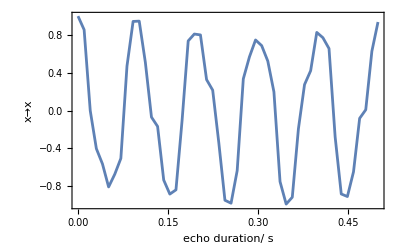

```mathematica
ListPlot[table,Joined->True,PlotRange->{-1,1},FrameLabel->{"echo duration/ s","x→x"}]
```

#### EnsembleAverage

EnsembleAverage may be used together with TransformationAmplitudeTable. The following example plots the offset dependence of a composite pulse, including also a range in rf amplitudes. The x-coordinates are converted to Hz:

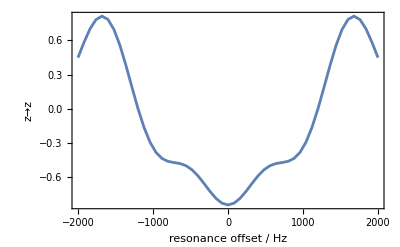

```mathematica
TransformationAmplitudeTable[
opI["z"]->opI["z"],
PulseSequence[{Pulse[{π/2,"x"}],Pulse[{π,"y"}],Pulse[{π/2,"x"}]},AmplitudeFactor->ampfac,NutationFrequency->2π 1 10^3],
{Ω,-2π 2 10^3,2π 2 10^3,{51}},EnsembleAverage->{ampfac,Range[0.5,1.5,0.1]},
BackgroundGenerator->Ω opI["z"],
TableCoordinates->Ω/(2π)
];
ListPlot[%,FrameLabel->{"resonance offset / Hz","z→z"}]
```

#### NormalizationFactor

The option NormalizationFactor→normfac may be used to divide the output of TransformationAmplitudeTable by normfac. The default value is 1.

The example below shows the result of two calculations, one using the default value of NormalizationFactor, and one with a user-specified value.

```mathematica
SetSpinSystem[1];
TransformationAmplitudeTable[opI["z"]->opI["z"],
Repeat[{2π opI["x"],1/2},n],
{n,0,10}
]
TransformationAmplitudeTable[opI["z"]->opI["z"],
Repeat[{2π opI["x"],1/2},n],
{n,0,10},
NormalizationFactor->2
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder].

{{0,1.},{1,-1.},{2,1.},{3,-1.},{4,1.},{5,-1.},{6,1.},{7,-1.},{8,1.},{9,-1.},{10,1.}}

{{0,0.5},{1,-0.5},{2,0.5},{3,-0.5},{4,0.5},{5,-0.5},{6,0.5},{7,-0.5},{8,0.5},{9,-0.5},{10,0.5}}

#### TransformationAmplitudeTable with 2 parameters

TransformationAmplitudeTable may also be used with 2 or more variable parameters.

The example below calculates the effect of resonance offset and rf amplitude errors on population inversion induced by a 90_x 180_y 90_x composite pulse, and plots the result using ContourPlot:

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

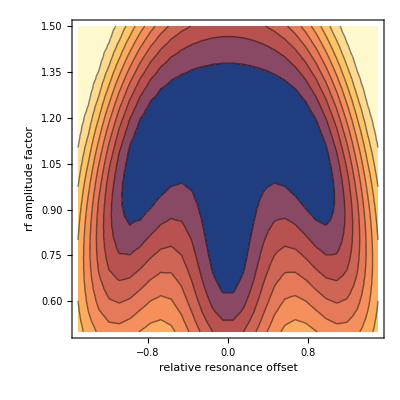

```mathematica
SetSpinSystem[1];
TransformationAmplitudeTable[
opI["z"]->opI["z"],
PulseSequence[{Pulse[{π/2,"x"}],Pulse[{π,"y"}],Pulse[{π/2,"x"}]},AmplitudeFactor->ϵ,NutationFrequency->2π],
{Ω,-1.5 2π,1.5 2π,{30}},
{ϵ,0.5,1.5,{30}},
BackgroundGenerator->Ω opI["z"],
TableCoordinates->{Ω/(2π),ϵ}
];
ListContourPlot[%,FrameLabel->{"relative resonance offset","rf amplitude factor"}]
```

TransformationAmplitudeTable supports any number of variable parameters, together with EnsembleAverage if needed.

## MaximizeTransformationAmplitude

MaximizeTransformationAmplitude enables numerical optimization of a TransformationAmplitude by adjusting the values of one or more parameters. A common application is to optimize the performance of a pulse sequence by adjusting pulse flip angles, phases, or the durations of delays.

#### basic functionality; unconstrained optimization

The basic syntax of MaximizeTransformationAmplitude is as follows:

MaximizeTransformationAmplitude[a→b, events, {{p1,p1ini},{p2,pini}..} options]

where a is the initial density operator, b is the target density operator, events contains the specifications for the evolution events, and {p1,p2..} are the parameters which are to be adjusted. The values {p1ini,p2ini..} are the starting values for the optimization.

MaximizeTransformationAmplitude searches for a local maximum, so the solution that it finds will depend on the starting point given by {p1ini,p2ini..}.

The output of MaximizeTransformationAmplitude has the form {val,rules} where val is the optimized value of the TransformationAmplitude, and rules specifies the optimized values of the parameters {p1,p2..}.

For example, the following syntax shows the optimization of a pulse flip angle in order to maximize the inversion of z-magnetization:

```mathematica
SetSpinSystem[1];
MaximizeTransformationAmplitude[
opI["z"]->-opI["z"],
Pulse[{β,"x"}],
{β,0.01}
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

MaximizeTransformationAmplitude::unconstr: Deploying FindMinimum without constraints.

MaximizeTransformationAmplitude::meth: Executing FindMinimum using Method → "InteriorPoint". See the usage message for FindMinimum for other possible values of Method.

{1.,{β→3.14159}}

The routine has optimized the flip angle to the value π = 180°, as shown as follows:

```mathematica
{val,rules}=%
(β/.rules)/°
```

{1.,{β→3.14159}}

180.

Note that the optimized value is +1, since the routine was instructed to maximize the conversion of I_z to -I_z.

The same optimization can give a different value when a different starting point is chosen:

```mathematica
{val,rules}=MaximizeTransformationAmplitude[
opI["z"]->-opI["z"],
Pulse[{β,"x"}],
{β,0.1}
]
(β/.rules)/°
```

MaximizeTransformationAmplitude::unconstr: Deploying FindMinimum without constraints.

MaximizeTransformationAmplitude::meth: Executing FindMinimum using Method → "InteriorPoint". See the usage message for FindMinimum for other possible values of Method.

{1.,{β→15.708}}

900.

In this case the surprising choice of 900° is generated. This is a valid solution although not the expected one. Constrained optimization can prevent such unexpected behaviour (see below):

#### basic functionality; constrained optimization

Constraints may be added by using the syntax:

MaximizeTransformationAmplitude[a→b, events, {{p1,p1ini,{p1min,p1max}},{p2,p2ini,{p2min,p2max}}..} options]

where the search is performed over a region constrained by the specified minimum and maximum values of the parameters.

For example, the following syntax shows the optimization of a pulse flip angle in order to maximize the inversion of z-magnetization, with the flip angle constrained to the range 0 to 2π:

```mathematica
SetSpinSystem[1];
{val,rules}=MaximizeTransformationAmplitude[
opI["z"]->-opI["z"],
Pulse[{β,"x"}],
{β,0.1,{0,2π}}
]
(β/.rules)/°
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

MaximizeTransformationAmplitude::constr: Deploying FindMinimum with constraints 0≤β≤2 π.

{1.,{β→3.14159}}

180.

This inhibits the generation of valid but wild solutions.

Another way of adding constraints is to use the ConstrainPositive option. This allows one to specify that one or more optimization parameters may only take positive values, which is commonly the case when, for example, a delay is optimized.

In the following example, a sequence of two pulses, separated by a delay, is optimized in order to invert the z-magnetization, under a given resonance offset. The flip angles and delay duration must always be positive, while the phase of the second pulse is not constrained:

```mathematica
SetSpinSystem[1];
{val,rules}=MaximizeTransformationAmplitude[
opI["z"]->-opI["z"],
{Pulse[{π/2,"x"}],
Delay[τ],
Pulse[{β,ϕ}]
},
{{β,π/10},{ϕ,0},{τ,0.001}},
BackgroundGenerator->2π opI["z"],
ConstrainPositive->{β,τ}
]
{β/°,ϕ/°,τ}/.rules
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

MaximizeTransformationAmplitude::constr: Deploying FindMinimum with constraints 0≤β≤∞&&-∞≤ϕ≤∞&&0≤τ≤∞.

{1.,{β→1.5708,ϕ→1247.73,τ→198.582}}

{90.,71489.5,198.582}

The crazy but valid solution for ϕ may again be avoided by using more explicit constraints:

```mathematica
SetSpinSystem[1];
{val,rules}=MaximizeTransformationAmplitude[
opI["z"]->-opI["z"],
{Pulse[{π/2,"x"}],
Delay[τ],
Pulse[{β,ϕ}]
},
{{β,π/10,{0,2π}},{ϕ,0,{-2π,2π}},{τ,0.001,{0,1}}},
BackgroundGenerator->2π opI["z"]
]
{β/°,ϕ/°,τ}/.rules
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

MaximizeTransformationAmplitude::constr: Deploying FindMinimum with constraints 0≤β≤2 π&&-2 π≤ϕ≤2 π&&0≤τ≤1.

{1.,{β→1.5708,ϕ→2.67018,τ→0.424973}}

{90.,152.99,0.424973}

The option values, including the BackgroundGenerator, may also depend on the optimization parameters. In the example below, the phase of the pulses are kept fixed, while the resonance offset is optimized:

```mathematica
SetSpinSystem[1];
{val,rules}=MaximizeTransformationAmplitude[
opI["z"]->-opI["z"],
{Pulse[{π/2,"x"}],
Delay[τ],
Pulse[{β,"y"}]
},
{{β,π/10,{0,2π}},{Ω,0,{-2π 10,2π 10}},{τ,0.001,{0,1}}},
BackgroundGenerator->Ω opI["z"]
]
{β/°,Ω/(2π),τ}/.rules
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

MaximizeTransformationAmplitude::constr: Deploying FindMinimum with constraints 0≤β≤2 π&&-20 π≤Ω≤20 π&&0≤τ≤1.

{1.,{β→1.5708,Ω→2.36242,τ→0.66491}}

{90.,0.375991,0.66491}

#### common problems

Sometimes the numeric search transgresses slightly into a forbidden region (such as negative delays) even when constraints are given. This generates a fatal error. An example is given below:

```mathematica
SetSpinSystem[1];MaximizeTransformationAmplitude[opI["z"]->-opI["z"],
{Pulse[{π/2,"x"}],Delay[τ],Pulse[{π/2,"y"}]},{τ,0,{0,1}},
BackgroundGenerator->2π opI["z"]
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

MaximizeTransformationAmplitude::constr: Deploying FindMinimum with constraints 0≤τ≤1.

Delay::negdur: Delay may not have a negative duration.

General::stop: Further output of Delay::negdur will be suppressed during this calculation.

FindMinimum::nrnum: The function value -$Failed is not a real number at {τ} = {-6.05545×10^-6}.

MaximizeTransformationAmplitude::fail: An event duration, or pulse flip angle, has transgressed into an unphysical region, causing MaximizeTransformationAmplitude to fail. Try again with a different starting point, or incorporate constraints on the parameters (see usage message for MaximizeTransformationAmplitude).

$Failed

This may usually be avoided by specifying an initial point which is not close to the bound of a forbidden region:

```mathematica
SetSpinSystem[1];MaximizeTransformationAmplitude[opI["z"]->-opI["z"],
{Pulse[{π/2,"x"}],Delay[τ],Pulse[{π/2,"y"}]},{τ,0.1,{0,1}},
BackgroundGenerator->2π opI["z"]
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

MaximizeTransformationAmplitude::constr: Deploying FindMinimum with constraints 0≤τ≤1.

{1.,{τ→0.25}}

#### optimization methods

MaximizeTransformationAmplitude deploys the Mathematica routine FindMinimum. This routine may use a variety of settings for the Method option (see the Mathematica documentation). This setting is passed down from the MaximizeTransformationAmplitude routine.

The cells below show a variety of methods applied to the same problem. The execution time is also shown and depends strongly on the Method which is used. Some methods are only applicable to unconstrained problems, and some methods run into problems for this particular example.

```mathematica
SetSpinSystem[1];
{time,{val,rules}}=Timing@MaximizeTransformationAmplitude[
opI["z"]->-opI["z"],
{RotationSuperoperator[{π/2,"x"}],
{None,τ},
RotationSuperoperator[{β,ϕ}]
},
{{β,π/10},{ϕ,0},{τ,0.1}},
BackgroundGenerator->2π opI["z"],
Method->"PrincipalAxis"
]
{β/°,ϕ/°,τ}/.rules
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

MaximizeTransformationAmplitude::unconstr: Deploying FindMinimum without constraints.

MaximizeTransformationAmplitude::meth: Executing FindMinimum using Method → "PrincipalAxis". See the usage message for FindMinimum for other possible values of Method.

{1.1066,{1.,{β→1.5708,ϕ→0.628319,τ→0.1}}}

{90.,36.,0.1}

## Signal1D

Signal1D calculates a uniformly sampled one-dimensional time-domain signal, specified by the number of sampling points, the sampling interval, the events during the signal evolution, and many other options.

#### basic functionality

The basic syntax of Signal1D is as follows:

Signal1D[{tmin,tmax,dt}, DetectionSpecifications, options]

where tmin and tmax are the minimum and maximum time points of the sampled signal, and δt is the spacing between sampling points.

The symbol DetectionSpecifications may be (1) a single evolution generator (a Hamiltonian, or a relaxation superoperator, or a combination of these), or (2) a list of events to be executed during signal detection. Case 1 is discussed here. Case 2 is discussed later.

A simple example of case 1, showing the simulation of an AB spectral pattern, is as follows:

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
signal=Signal1D[{0,1,1/200},H0]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 1.46587 rad s^-1.

Signal[{0,1.,5.×10^-3}, {Lorentzian,<<4>>}]

Signal1D reports the algorithm chosen for the particular simulation problem, reports that 1.47 Hz Lorentzian line broadening has been applied automatically, and that the number of points has been adjusted to get an even number, which is required for the fast Fourier transform algorithm.

#### Signal and FT

The output of Signal1D is a Signal object (see part 7 of the documentation for more details).

In the case below, the output format indicates that the signal runs from time point 0 to time 195 ms, in steps of 5 ms, and contains 4 Lorentzian peaks.

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
signal=Signal1D[{0,0.2,5 10^-3},H0]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 7.32936 rad s^-1.

Signal[{0,200.×10^-3,5.×10^-3}, {Lorentzian,<<4>>}]

The real (Re) or imaginary (Im) parts of the Signal object may be plotted using ListPlot:

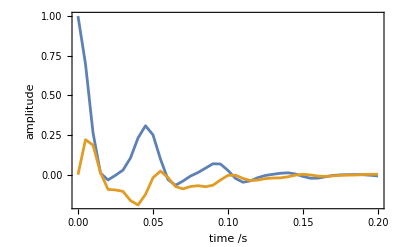

```mathematica
ListPlot[{Re[signal],Im[signal]},Joined->True,PlotRange->All,FrameLabel->{"time /s","amplitude"}]
```

A Signal object may be converted into the frequency domain by applying the complex Fourier transform routine FT (this is a SpinDynamica routine which is an extension of the Mathematica routine Fourier).

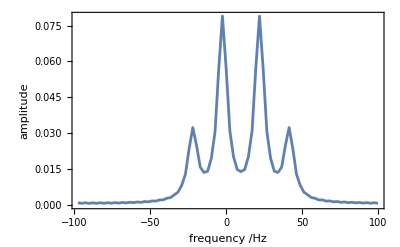

```mathematica
ListPlot[
Re[FT[signal]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

The “@” syntax in Mathematica may also be used:

```mathematica
ListPlot[
Re@FT@signal,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

-Graphics-

The frequency coordinates generated by FT are in Hz.

See part 7 of the documentation for more details on Signal and FT.

#### LineBroadening

The option LineBroadening specifies the full-width-at-half-height of Lorentzian linebroadening, in units of rad s^-1.

The default setting is Automatic, which sets the LineBroadening so as to reduce the signal envelope to 1% at the end of the time-domain signal. The setting LineBroadening→None may be used to eliminate the linebroadening, for example:

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
signalnobroadening=Signal1D[{0,1,1/200},H0,LineBroadening->None]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal[{0,1.,5.×10^-3}, {Lorentzian,<<4>>}]

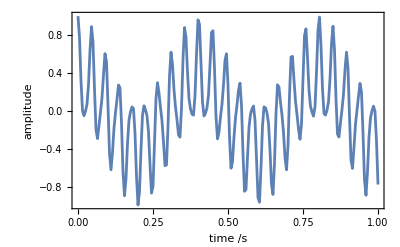

```mathematica
ListPlot[Re[signalnobroadening],Joined->True,PlotRange->All,FrameLabel->{"time /s","amplitude"}]
```

LineBroadening may also be applied to the signal at the time of the Fourier transform, for example:

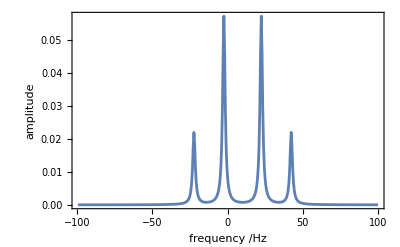

```mathematica
ListPlot[
Re[FT[signalnobroadening,LineBroadening->2π 2]],Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

A numerical value may also be given for LineBroadening. This specifies the full-width-at-half-height for the spectrum after Lorentzian linebroadening, in units of rad s^-1:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

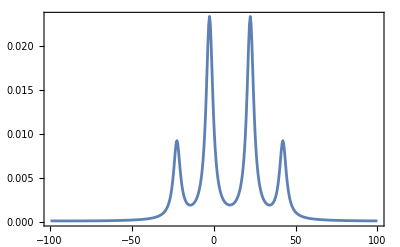

```mathematica
ListPlot[
Re@FT@Signal1D[{0,1,1/200},H0,LineBroadening->2π 5,FrameLabel->{"frequency /Hz","amplitude"}]
]
```

See part 7 of the documentation for more details.

#### Specifying the sampling using timing parameters

The first argument to Signal1D may be the form {tmin, tmax, δt} where tmin is the time coordinate of the first signal sample, tmax is the time coordinate of the last sample, and δt is the sampling interval (“dwell time”).

In most cases, tmin is 0.

The inverse of δt is the bandwidth of the spectrum after the Fourier transform, in Hz.

The inverse of tmax-tmin is the digital resolution of the spectrum after the Fourier transform, in Hz.

These parameters should be adjusted to bring the desired spectrum into the spectral bandwidth, without folding.

As an example, the settings below give a spectrum of bandwidth 200 Hz, and digital resolution of 1 Hz:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 1.46587 rad s^-1.

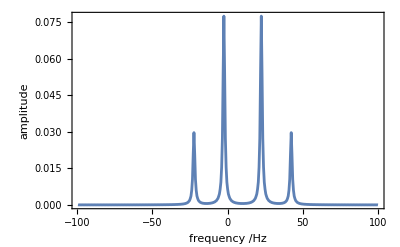

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
ListPlot[Re@FT@Signal1D[{0,1,1/200},H0],FrameLabel->{"frequency /Hz","amplitude"}]
```

Increasing the value of δt decreases the spectral bandwidth:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 1.46587 rad s^-1.

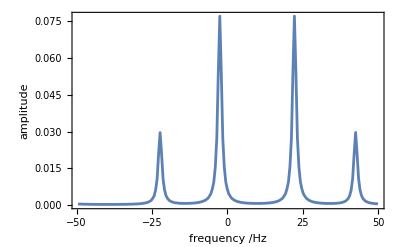

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
ListPlot[Re@FT@Signal1D[{0,1,1/100},H0],FrameLabel->{"frequency /Hz","amplitude"}]
```

A further decrease causes folding:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 1.46587 rad s^-1.

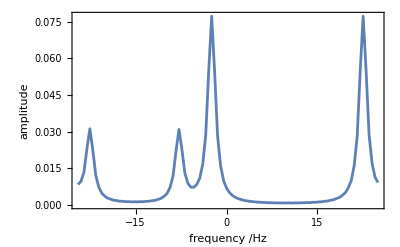

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
ListPlot[Re@FT@Signal1D[{0,1,1/50},H0],FrameLabel->{"frequency /Hz","amplitude"}]
```

Increasing tmax improves the digital resolution, but without affecting the folding:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 146.587×10^-3 rad s^-1.

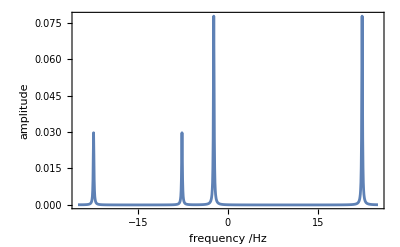

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
ListPlot[Re@FT@Signal1D[{0,10,1/50},H0],FrameLabel->{"frequency /Hz","amplitude"}]
```

The folding must be corrected by reducing the value of δt:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 146.587×10^-3 rad s^-1.

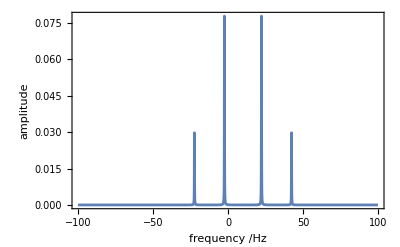

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
ListPlot[Re@FT@Signal1D[{0,10,1/200},H0],FrameLabel->{"frequency /Hz","amplitude"}]
```

If Signal1D generates a spectrum of unexpected appearance, the timing parameters should be examined carefully to see if the spectrum is folded.

#### Specifying the sampling using the spectral bandwidth and the number of points

It is also possible to specify the spectral bandwidth (in rad s^-1) and the number of points, using the syntax {tmin,{ωSW,npoints}}. In the example below, the spectral bandwidth is specified as 200 Hz and the number of points as 1k:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 286.863×10^-3 rad s^-1.

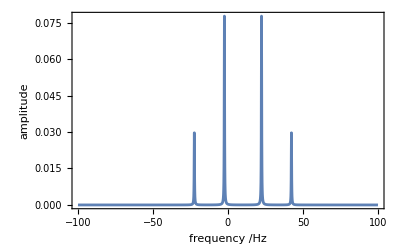

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
ListPlot[Re@FT@Signal1D[{0,{2π 200, "1k"}},H0],FrameLabel->{"frequency /Hz","amplitude"}]
```

The value of tmin defaults to zero, if omitted:

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
ListPlot[Re@FT@Signal1D[{{2π 200, "1k"}},H0],FrameLabel->{"frequency /Hz","amplitude"}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 286.863×10^-3 rad s^-1.

-Graphics-

In many cases, this is the most convenient syntax for Signal1D.

#### Observable

The option Observable may be set to 
	▪ an operator, or 
	▪ one or more spin system labels, or
	▪ All

The default value of Observable is All, which implies that all spins give rise to the quadrature NMR signal.

If Observable is set to a list of spins {j,k..}, then the observable operator for quadrature signal detection is set to -(i/2)(I_j^-+I_k^-+..).

For example, consider a 3 spin system, in which spins #1 and #2 are I-spins, while spin #3 is an S-spin. A Hamiltonian is set up for this heteronuclear spin system:

```mathematica
SetSpinSystem[3];
H0 = 2π 100 opI[1,"z"]+2π (-120) opI[2,"z"]+2π 30 opI[3,"z"]+
2π 6 opI[1].opI[2]+2π 4 opI[1].opI[3]+2π 5 opI[2].opI[3];
Ispins={1,2};
Sspins={3};
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

By default, all spins are detected at the same time:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 430.295×10^-3 rad s^-1.

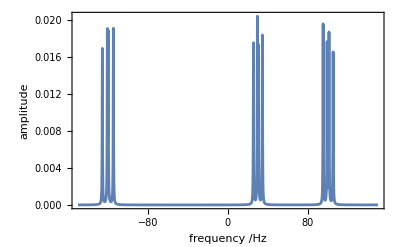

```mathematica
ListPlot[Re@FT@Signal1D[{{2π 300,"1k"}},H0],PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

Detection of only the I-spins is enforced as follows:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 430.295×10^-3 rad s^-1.

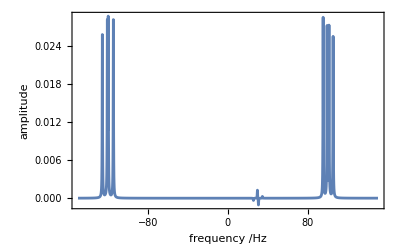

```mathematica
ListPlot[Re@FT@Signal1D[{{2π 300,"1k"}},H0,Observable->Ispins],PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

Detection of only the S-spins is enforced as follows:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 430.295×10^-3 rad s^-1.

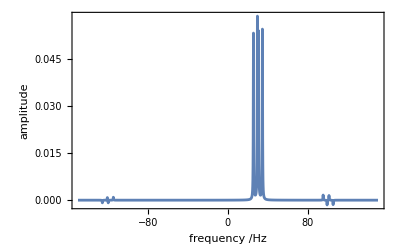

```mathematica
ListPlot[Re@FT@Signal1D[{{2π 300,"1k"}},H0,Observable->Sspins],PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

In these examples, small peaks are obtained at the positions of the “wrong” spins, as a by-product of the strong coupling. These are not computational errors.

In general, any operator may be used as the observable:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 430.295×10^-3 rad s^-1.

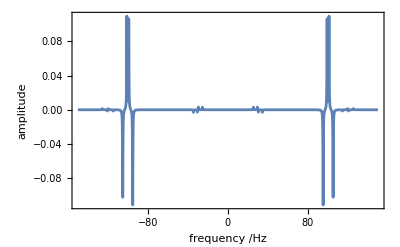

```mathematica
ListPlot[Re@FT@Signal1D[{{2π 300,"1k"}},H0,Observable->opI[1,"y"].opI[2,"z"].opI[3,"z"]],PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

#### BackgroundGenerator: non-periodic case

The option BackgroundGenerator sets the background evolution generator for the calculation. This evolution generator is combined with any other events during the generation of the signal.

This example uses BackgroundGenerator to simulate the spectrum of a single S-spin coupled to two I-spins

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 430.295×10^-3 rad s^-1.

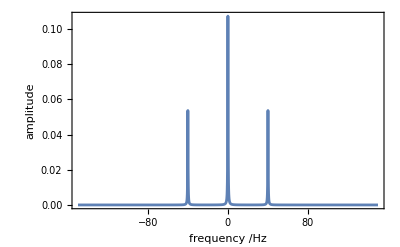

```mathematica
SetSpinSystem[3];
Ispins={1,2};Sspins={3};
H0 = 2π 6 opI[1].opI[2]+2π 40 opI[1,"z"].opI[3,"z"]+2π 40 opI[2,"z"].opI[3,"z"];
ListPlot[Re@FT@
Signal1D[{{2π 300,"1k"}},
BackgroundGenerator->H0,
Observable->Sspins
],
PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

An additional Hamiltonian may be specified to simulate the effect of a continuous decoupling field applied to the I-spins, throughout the entire detection interval. This Hamiltonian is combined with the BackgroundGenerator

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 430.295×10^-3 rad s^-1.

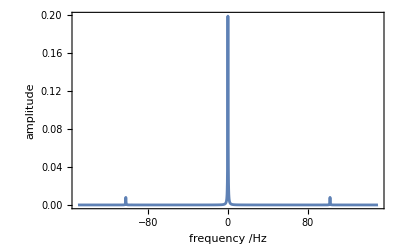

```mathematica
SetSpinSystem[3];
Ispins={1,2};Sspins={3};
H0 = 2π 6 opI[1].opI[2]+2π 40 opI[1,"z"].opI[3,"z"]+2π 40 opI[2,"z"].opI[3,"z"];
Hdec=2π 100 opI[Ispins,"x"];
ListPlot[Re@FT@
Signal1D[{{2π 300,"1k"}},
Hdec,
BackgroundGenerator->H0,
Observable->Sspins
],
PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

#### BackgroundGenerator: periodic case

BackgroundGenerator may also be a PeriodicFunction. In the example below, a periodic cosine-modulated Hamiltonian is applied throughout the signal detection:

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

Signal1D::reportscm: Using SignalCalculationMethod → COMPUTE

Signal1D::autolb: Using LineBroadening → 2π × 14.3432 rad s^-1.

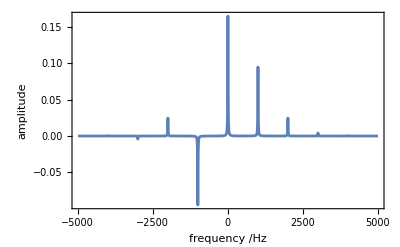

```mathematica
SetSpinSystem[1];
ListPlot[
Re[FT[
Signal1D[{{2π 10 10^3,"1k"}},
BackgroundGenerator->PeriodicFunction[t,10^-3,2π 10^3 opI["z"]Cos[2π 10^3 t]]
]
]],
Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
```

Note the adjustment of the sampling interval, and that the periodic time-dependent modulation gives rise to modulation sidebands in the spectrum. Spinning sidebands in liquids and solids may be simulated this way.

In the case of periodic background generators, the option CarouselAverage→True may be used to compute the average over all modulation phases (see M. H. Levitt, “Why do Spinning Sidebands Have the Same Phase?,” J. Magn. Reson. 82, 427 (1989)):

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → COMPUTE

Signal1D::autolb: Using LineBroadening → 2π × 14.3432 rad s^-1.

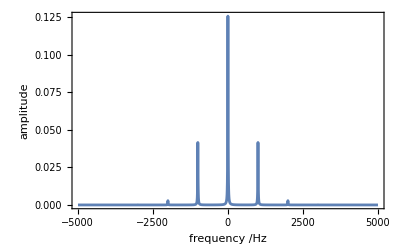

```mathematica
SetSpinSystem[1];
ListPlot[
Re[FT[
Signal1D[{{2π 10 10^3,"1k"}},
BackgroundGenerator->PeriodicFunction[t,10^-3,2π 10^3 opI["z"]Cos[2π 10^3 t]],
CarouselAverage->True
]
]],
Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
```

#### Preparation

The option Preparation is used to define the preparation sequence applied to the spin density operator, before the signal is detected.

The default value of Preparation is Pulse[{π/2,”x”}], implying an ideal 90° pulse of phase 0, applied to all spins in the system.

For example, consider a coupled 3 spin system:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 573.726×10^-3 rad s^-1.

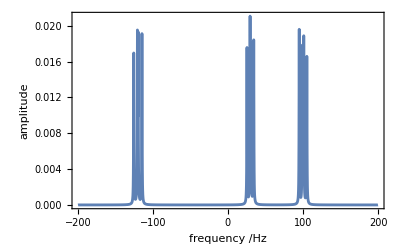

```mathematica
SetSpinSystem[3];
H0 = 2π 100 opI[1,"z"]+2π (-120) opI[2,"z"]+2π 30 opI[3,"z"]+
2π 6 opI[1].opI[2]+2π 4 opI[1].opI[3]+2π 5 opI[2].opI[3];
ListPlot[Re@FT@Signal1D[{{2π 400,1024}},BackgroundGenerator->H0],PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

The phase of the preparation pulse may be changed as follows:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 573.726×10^-3 rad s^-1.

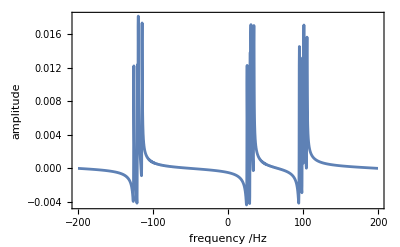

```mathematica
ListPlot[Re@FT@Signal1D[
{{2π 400,1024}},
BackgroundGenerator->H0,
Preparation->(Pulse[{π/2,π/4}])
],
PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

A weak preparation pulse may be defined by using the Pulse routine, but including a specification for either PulseDuration or NutationFrequency. In the example below, the nutation frequency of the pulse is set to 5 Hz, leading to a high degree of frequency selectivity:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 573.726×10^-3 rad s^-1.

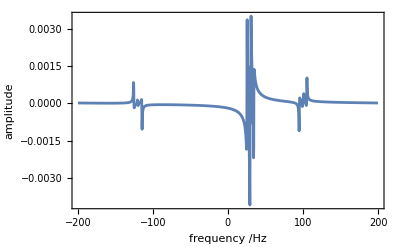

```mathematica
ListPlot[Re@FT@Signal1D[
{{2π 400,1024}},
BackgroundGenerator->H0,
Preparation->Pulse[{π/2,"x"},NutationFrequency->2π 5]
],
PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

Any valid sequence of events may be used for the preparation sequence.

It is possible to use a different BackgroundGenerator for the spin dynamics during the preparation sequence, and the signal evolution events, by using the syntax BackgroundGenerator→{prepbackg,detbackg}, where prepbackg is the BackgroundGenerator during the preparation, and is the detbackg is the BackgroundGenerator during the signal detection.

The example below uses this feature to effectively shift the rf carrier frequency during the preparation sequence:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 573.726×10^-3 rad s^-1.

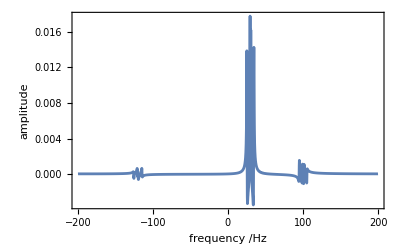

```mathematica
ListPlot[Re@FT@Signal1D[
{{2π 400,1024}},
BackgroundGenerator->{H0-2π 30 opI["z"],H0},
Preparation->{Pulse[{π/2,"x"},NutationFrequency->2π 5]}
],
PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

#### InitialDensityOperator

The option InitialDensityOperator is used to define the spin density operator to which the Preparation is applied.

The default value of InitialDensityOperator is opI[“z”], implying equal z-polarization for all spins in the system.

For example, consider a coupled 2 spin system:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 573.726×10^-3 rad s^-1.

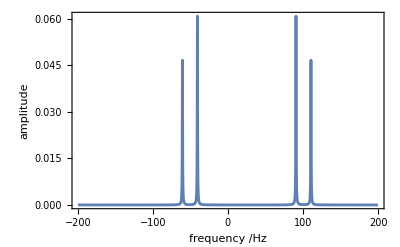

```mathematica
SetSpinSystem[2];
H0 = 2π 100 opI[1,"z"]+2π (-50) opI[2,"z"]+2π 20 opI[1].opI[2];
ListPlot[
Re@FT@Signal1D[
{{2π 400,1024}},
BackgroundGenerator->H0
],
PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

The effect of inverting the polarization of spins #2 before the preparation pulse is applied, may be simulated as follows:

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 573.726×10^-3 rad s^-1.

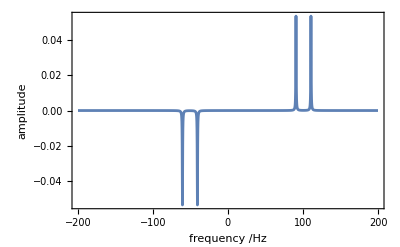

```mathematica
ListPlot[
Re@FT@Signal1D[
{{2π 400,1024}},
BackgroundGenerator->H0,
InitialDensityOperator->opI[1,"z"]-opI[2,"z"]
],
PlotRange->All, Joined->True,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}]
```

#### detection events

Signal1D may be called with the following syntax:

Signal1D[{tmin,tmax,dt}, events, options]

where events specifies the list of events happening during the signal detection. This allows simulation of the magnetic resonance signal during a pulse sequence. In the following simulation an rf field is turned on during the first 0.1 second of the signal detection. The rest of the signal detection interval is automatically padded with an event of the form {None, τ}:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Direct

Signal1D::autolb: Using LineBroadening → 2π × 1.47327 rad s^-1.

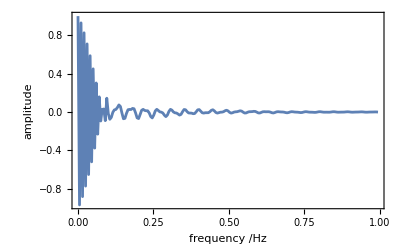

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
signal=Signal1D[
{0,1,{200}},
{{2π 100 opI["x"],0.1}},
BackgroundGenerator->H0
];
ListPlot[
Re[signal],
Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
```

Repeat may be used to generate a repetitive pulse sequence starting at the beginning of the signal detection. In the example below, a set of 2 events is repeated 10 times at the beginning of signal detection.

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Direct

Signal1D::autolb: Using LineBroadening → 2π × 1.47327 rad s^-1.

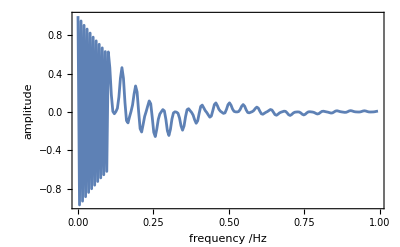

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
signal=
Signal1D[{0,1,{200}},
Repeat[
{{-2π 100 opI["x"],5 10^-3},{2π 100 opI["x"],5 10^-3}},
10
],
BackgroundGenerator->H0
];
ListPlot[
Re[signal],
Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
```

If the number of repetitions in Repeat is omitted, the repetitions are assumed to fill out the entire detection interval. The fast COMPUTE algorithm is used in this case:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → COMPUTE

Signal1D::newδt: Sampling interval has been adjusted to 5.×10^-3 s for compatibility with the periodicity of the specified events and/or the BackgroundGenerator.

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 1.46587 rad s^-1.

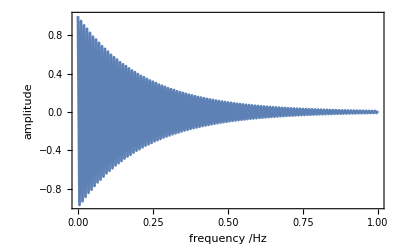

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
signal=
Signal1D[{0,1,{200}},
Repeat[
{{-2π 100 opI["x"],5 10^-3},{2π 100 opI["x"],5 10^-3}}
],
BackgroundGenerator->H0
];
ListPlot[
Re[signal],
Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
```

Syntax of this form may be used to simulate decoupling sequences. The following instructions simulate the effect of repetitive 90_x180_y90_x composite pulses applied to the I-spins while the S-spins are detected:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → COMPUTE

Signal1D::newδt: Sampling interval has been adjusted to 125.×10^-6 s for compatibility with the periodicity of the specified events and/or the BackgroundGenerator.

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 2.93174 rad s^-1.

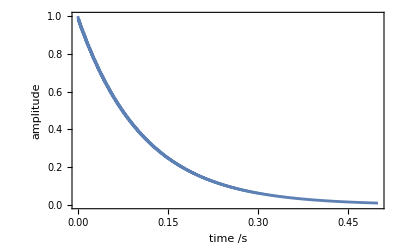

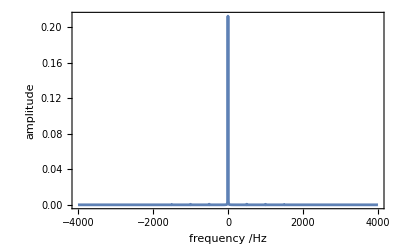

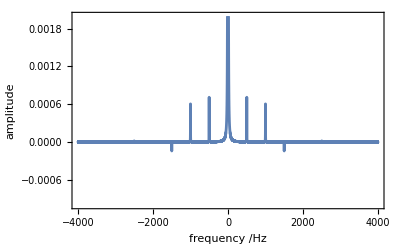

```mathematica
SetSpinSystem[2]; Ispins={1}; Sspins={2};
H0=2π 150 opI[1,"z"].opI[2,"z"];
ωnutI=2π 10^3; 
τ360I=2π/ωnutI; τ90I=τ360I/4; τ180I=τ360I/2;
signal=
Signal1D[{0,0.5,{4096}},
Repeat[
{{ωnutI opI[Ispins,"x"],τ90I},{ωnutI opI[Ispins,"y"],τ180I},
{ωnutI opI[Ispins,"x"],τ90I}
}
],
BackgroundGenerator->H0,
Observable->Sspins
];
ListPlot[
Re[signal],
Joined->True,PlotRange->All,Frame->True,FrameLabel->{"time /s","amplitude"}
]
ListPlot[
Re@FT[signal],
Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
ListPlot[
Re@FT[signal],
Joined->True,PlotRange->{-0.001,0.002},Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
```

Note the weak cycling sidebands in the spectrum.

Averaging over all possible relative time shifts of the repeated detection events and the signal detection is accomplished using the option CarouselAverage→True:

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → COMPUTE

Signal1D::newδt: Sampling interval has been adjusted to 125.×10^-6 s for compatibility with the periodicity of the specified events and/or the BackgroundGenerator.

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 2.93174 rad s^-1.

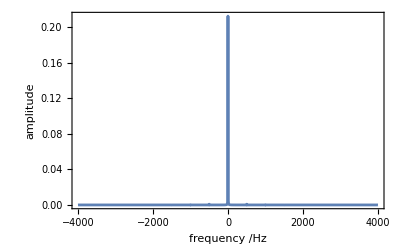

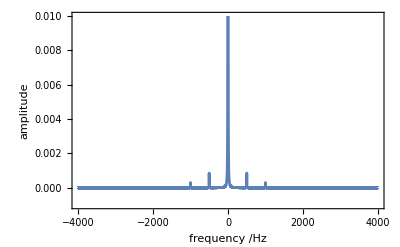

```mathematica
SetSpinSystem[2]; Ispins={1}; Sspins={2};
H0=2π 150 opI[1,"z"].opI[2,"z"];
ωnutI=2π 10^3; 
τ360I=2π/ωnutI; τ90I=τ360I/4; τ180I=τ360I/2;
signal=
Signal1D[{0,0.5,{4096}},
Repeat[
{{ωnutI opI[Ispins,"x"],τ90I},{ωnutI opI[Ispins,"y"],τ180I},
{ωnutI opI[Ispins,"x"],τ90I}
}
],
BackgroundGenerator->H0,
Observable->Sspins,
CarouselAverage->True
];
ListPlot[
Re@FT[signal],
Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
ListPlot[
Re@FT[signal],
Joined->True,PlotRange->{-0.001,0.01},Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
```

#### EnsembleAverage

The EnsembleAverage option may be used to take the weighted sum of many signal calculations.

For example, the effect of a linear field gradient on a rectangular sample may be simulated by constructing a uniform distribution of resonance offsets:

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 1.47327 rad s^-1.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder].

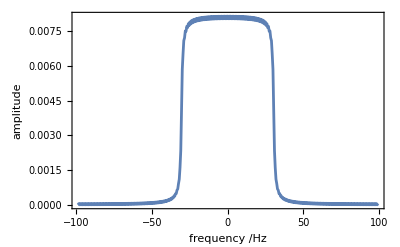

```mathematica
SetSpinSystem[1];
ListPlot[
Re@FT@Signal1D[
{0,1,{200}},
BackgroundGenerator->ωG opI["z"],
EnsembleAverage->{ωG,2π Range[-30,30,1]}
],
Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
```

A Pake pattern for coupled spin-1/2 pairs may be simulated by taking the ensemble average over the angle β between the internuclear vector and the external magnetic field. Note that cosβ is used as the random variable instead of β, since an isotropic distribution of molecular orientations corresponds to a uniform distribution of cosβ in the range [-1,1].

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 573.726×10^-3 rad s^-1.

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

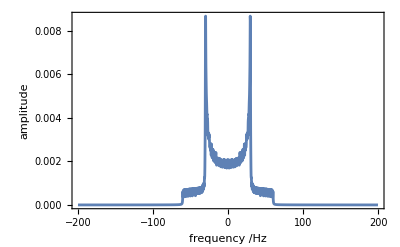

```mathematica
SetSpinSystem[2];
ListPlot[
Re@FT@Signal1D[
{{2π 400,1024}},
BackgroundGenerator->2π 40(3opI[1,"z"].opI[2,"z"]-opI[1].opI[2])(3 cosβ^2-1)/2,
EnsembleAverage->{cosβ,Range[-1,1,1/200]}
],
Joined->True,PlotRange->All,Frame->True,FrameLabel->{"frequency /Hz","amplitude"}
]
```

#### NormalizationFactor

The option NormalizationFactor→normfac may be used to divide the output of Signal1D by normfac. The default value is 1.

The example below shows the result of two calculations, one using the default value of NormalizationFactor, and one with a user-specified value.

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::autolb: Using LineBroadening → 2π × 2.96136 rad s^-1.

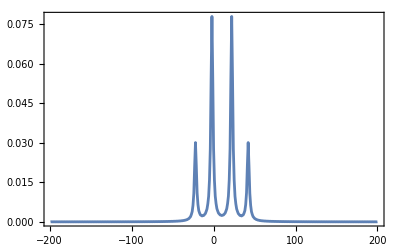

Signal1D::reportscm: Using SignalCalculationMethod → Diagonalization

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 1.46587 rad s^-1.

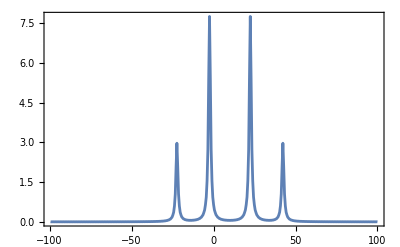

```mathematica
SetSpinSystem[2];
H0=2π 30 opI[1,"z"]+2π (-10) opI[2,"z"]+2π 20 opI[1].opI[2];
ListPlot@Re@FT@Signal1D[{{2π 400,200}},H0]
ListPlot@Re@FT@Signal1D[{0,1,1/200},H0,NormalizationFactor->1/100]
```

#### SignalCalculationMethod

Signal1D has a choice of three different computational algorithms, governed by the option SignalCalculationMethod. The default is SignalCalculationMethod→Automatic, in which case the routine tries to determine the most appropriate algorithm itself.

SignalCalculationMethod→"Direct" is the most general method. A Trajectory calculation is performed, and sampled at the specified set of times.

SignalCalculationMethod → "Diagonalization" is appropriate when a single, time-independent evolution generator spans the whole sampling interval.

SignalCalculationMethod → "COMPUTE" is appropriate for periodic time-dependent problems.  References: M. Edén, Y. K. Lee and M. H. Levitt, J. Magn. Reson. A 120, 56 (1996); M. H. Levitt and M. Edén, Mol. Phys. 95, 879-890 (1998); M. Hohwy, H. Bildsøe, H. J. Jakobsen and N. C. Nielsen, J. Magn. Reson. 136, 6-14 (1999); M. Helmle et al, J. Magn. Reson. 140, 379-403 (1999).

The COMPUTE algorithm sometimes requires adjustment of the sampling interval to be compatible with the period. The routine reports on this adjustment.

SignalCalculationMethod → “COMPUTE”  may be combined with the option CarouselAverage→True.

Signal1D provides a message indicating which method has been chosen, unless the option ReportSignalCalculationMethod is set to False. The message may be disabled for the whole session by executing SetOptions[Signal1D, ReportSignalCalculationMethod→False].

## low-level propagation routines

High-level routines such as Trajectory, TransformationAmplitude, and Signal1D use a set of low-level numerical propagation routines, which are documented here.

### NPropagate

NPropagate propagates a spin density operator through a series of events. The event specifications, and use of BackgroundGenerator and other options, are the same as in the routines above. The output of the routine is the final value of the spin density operator.

The general syntax is NPropagate[events, options][ρini] where ρini is the initial density operator.

The example below propagates a spin density operator under a series of events:

```mathematica
SetSpinSystem[1];
op=NPropagate[
{{2π opI["x"],1/4},
{2π opI["y"],1/2},
{2π opI["x"],1/4}}
][opI["z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

Operator[<<..>>, OperatorType→Hermitian ]

The resulting operator may be set into a readable form using ExpressOperator

```mathematica
ExpressOperator[op]
```

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder].

-1. I_(1z)

### NPropagationOperator

NPropagationOperator determines the overall propagation operator (propagator) of a series of events. The event specifications, and use of BackgroundGenerator and other options, are the same as in the routines above. The output of the routine is of the form Operator (see part 3 of the documentation).

The general syntax is NPropagationOperator[events, options].

The example below calculates the propagator of a series of events:

```mathematica
SetSpinSystem[1];
propagator=NPropagationOperator[
{{2π opI["x"],1/4},
{2π opI["y"],1/2},
{2π opI["x"],1/4}}
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

Operator[<<..>> , Assumptions→{OperatorType→"Unitary"}]

The resulting propagator may be set into a readable form using ExpressOperator

```mathematica
ExpressOperator[propagator]
```

1. I_1^--1. I_1^+

The matrix representation of the propagator may be calculated in any desired basis:

```mathematica
MatrixRepresentation[propagator,ZeemanBasis[]]//MatrixForm//Chop
```

(0 | -1.
1. | 0)

```mathematica
MatrixRepresentation[propagator,Eigenbasis[opI["x"]]]//MatrixForm//Chop
```

(0 | 1.
-1. | 0)

the propagator may be applied to a ket:

```mathematica
propagator[Ket["α"]];
Chop[%]
```

1. |β⟩

### NPropagationSuperoperator

NPropagationSuperoperator determines the overall propagation superoperator (superpropagator) of a series of events. The event specifications, and use of BackgroundGenerator and other options, are the same as in the routines above. The output of the routine is of the form Superoperator (see part 4 of the documentation).

The general syntax is NPropagationSuperoperator[events, options].

The example below calculates the propagation superoperator of a series of events:

```mathematica
SetSpinSystem[1];
superpropagator=NPropagationSuperoperator[
{{2π opI["x"],1/4},
{2π opI["y"],1/2},
{2π opI["x"],1/4}}
]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

Superoperator[<<..>>, SuperoperatorType→Undefined]

The matrix representation of the propagation superoperator may be calculated in any desired operator basis (see part 4 of the documentation):

```mathematica
SuperoperatorMatrixRepresentation[
superpropagator,CartesianProductOperatorBasis[]]//MatrixForm//Chop
```

(1. | 0 | 0 | 0
0 | -1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | -1.)

```mathematica
SuperoperatorMatrixRepresentation[
superpropagator,ShiftAndZOperatorBasis[]]//MatrixForm//Chop
```

(0 | 0 | 0 | -1.
0 | -1. | 0 | 0
0 | 0 | 1. | 0
-1. | 0 | 0 | 0)

the superpropagator may be applied to an operator:

```mathematica
superpropagator[opI["z"]];
N@Chop@%
```

-1. I_(1z)